## Model Setup

```mathematica
wm = ResourceFunction["WolframModel"];
plot = ResourceFunction["WolframModelPlot"];
randomRule = ResourceFunction["RandomWolframModel"];
```

```mathematica
steps=10;
maxValue = 3;
maxVertices=3;
```

```mathematica
randomSignature[maxRelations_, maxElements_, maxPieces_] := 
	Rule @@ Table[
		Table[
			{RandomInteger[{1, maxRelations}], RandomInteger[{1, maxElements}]},
			RandomInteger[{1, maxPieces}]
		], 
		2
	]
```

```mathematica
signature={{2,2}}->{{4,2}};
init = Array[Function[1],signature[[1]][[1]]];
rule = {{{1,2},{1,3}}->{{1,4},{4,5},{5,2},{3,5}}};
```

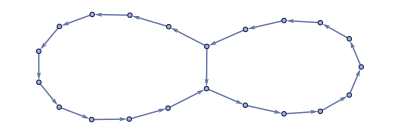

```mathematica
wm[rule, init, steps, "FinalStatePlot"]
```

## Mutations

### Simplest case: retain signature, replace only elements with same range

```mathematica
selectElement[rule_]:=
Module[{replacement, side, edge, vertex, x},
replacement=RandomInteger[{1, Length[rule]}];
x = rule[[replacement]];
side = RandomInteger[{1, 2}];
x = x[[side]];
edge = RandomInteger[{1, Length[x]}];
x = x[[edge]];
vertex = RandomInteger[{1, Length[x]}];
{replacement, side, edge, vertex}
]
```

```mathematica
maxElement[rule_]:=Max[Flatten[List@@@rule]]
```

```mathematica
replaceRandomElementOld[rule_]:=
Module[{pos=selectElement[rule]},
ReplacePart[rule, pos->
RandomChoice[Delete[Range[1,maxElement[rule]],Extract[rule, pos]]
]]]
```

#### Better version - uniform choice of elements

```mathematica
replaceRandomElement[rule_]:=
Module[{pos, elem, choices},
pos = RandomChoice[Position[rule, _, {4}, Heads->False]];
elem = Extract[rule, pos];
choices = Delete[Range[1, maxElement[rule]], elem];
ReplacePart[rule, pos->RandomChoice[choices]]
]
```

#### Evolution

```mathematica
evolve[startRule_, fitnessFunction_, nGenerations_, maxTries_:10] :=
Block[
{rule, fitness, newRule, newFitness},
NestList[CompoundExpression[
Do[
newRule=replaceRandomElement[First[#]];
newFitness=fitnessFunction[newRule];
If[newFitness >= Last[#], rule=newRule;fitness=newFitness;Break],
maxTries
],
{rule, fitness}]&,
{startRule, fitnessFunction[startRule]},
nGenerations]
]
```

## Fitness Functions

```mathematica
ruleDimension[rule_, nSteps_]:=graphDimension[Graph[wm[rule, {{1,1},{1,1}}, nSteps, "FinalState"]]]
```

```mathematica
graphDimension[graph_] :=
If[ConnectedGraphQ[graph],
 	ResourceFunction["WolframHausdorffDimension"][graph,All, "AllDimensions","VertexMethod" -> Max],
0] // If[NumberQ[#], #, 0]&
```

```mathematica
nearnessTo3D[rule_]:=-Abs[ruleDimension[rule, 7] -3]
```

```mathematica
ruleDimension[rule, 7]
```

1.6445

```mathematica
(* average ratio between numbers of vertices on successive steps *)
(* 0 for non-connected final graphs *)
vertexGrowthRate[rule_]:=
With[{evolution=wm[rule, init, 7]},
If[ConnectedGraphQ[Graph[evolution["FinalState"]]],
N[Mean[
Ratios[
evolution["VertexCountList"]//
Function[nVertices, PadRight[nVertices, 6, Last@nVertices]]
]]],
0]
]
```

```mathematica
edgeGrowthRate[rule_]:=
With[{evolution=wm[rule, init, 7]},
If[ConnectedGraphQ[evolution["FinalState"]],
N[Mean[
Ratios[
evolution["EdgeCountList"]//
Function[nEdges, PadRight[nEdges, 6, Last@nEdges]]
]]],
0]
]
```

## Compare Evolutions

```mathematica
graphRule[rule_]:=wm[rule, init, 7, "FinalStatePlot"]
```

```mathematica
compareEvolutions[evolutions_]:=
Column[Function[evolution, Row[Labeled[graphRule[First[#]], Last[#]]&/@evolution]]/@ evolutions]
```

```mathematica
evolutions = ParallelMap[Function[rule, evolve[rule, Function[r, -Abs[ruleDimension[r, 7]-3]], 5]] , Table[rule, 5]];
```

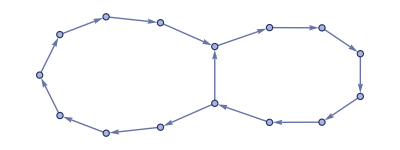
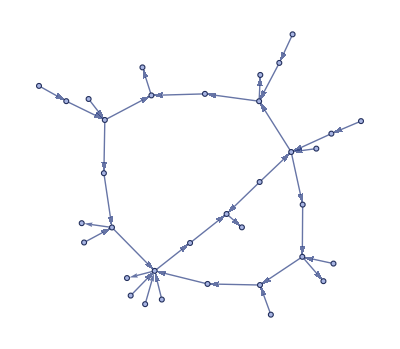
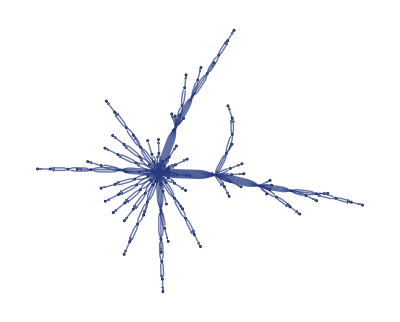
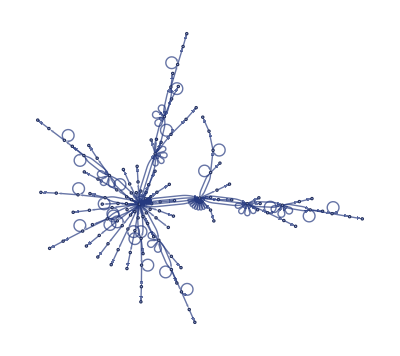
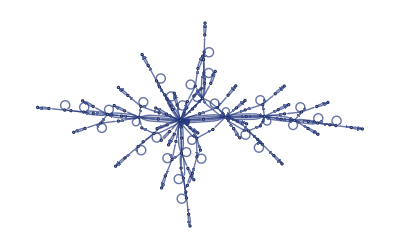
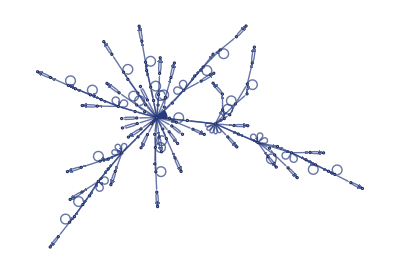
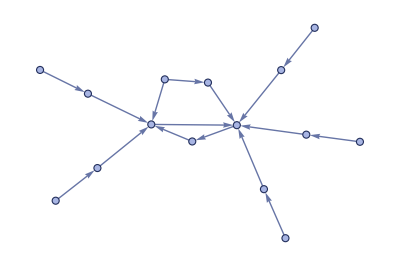
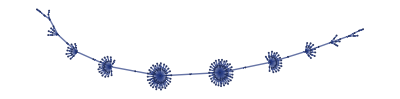
-Graphics--1.3555-Graphics--0.555291-Graphics--0.483024-Graphics--0.483024-Graphics--0.0318664-Graphics--0.0318664
-Graphics--1.3555-Graphics--0.892033-Graphics--0.23278-Graphics--0.23278-Graphics--0.23278-Graphics--0.23278
-Graphics--1.3555-Graphics--0.724877-Graphics--0.552771-Graphics--0.552771-Graphics--0.552771-Graphics--0.152104
-Graphics--1.3555-Graphics--1.3555-Graphics--1.266-Graphics--0.898989-Graphics--0.338656-Graphics--0.119347
-Graphics--1.3555-Graphics--1.19322-Graphics--1.13607-Graphics--0.59494-Graphics--0.380337-Graphics--0.288629

```mathematica
compareEvolutions[evolutions]
```

```mathematica
ListLinePlot[Function[evo,Callout[Last[#], graphRule[First[#]]]&/@evo]/@evolutions]
```

-Graphics-

## Animate evolution of single rule

```mathematica
coolRule
```

{{{1,2},{5,3}}→{{1,4},{4,2},{5,4},{3,4}}}

```mathematica
graphRule[coolRule]
```

-Graphics-

```mathematica
WolframModel[coolRule,
```

```mathematica
[Graph[wm[rule, {{1,1},{1,1}}, nSteps, "FinalState"]]]
```

```mathematica
ruleEvo = wm[coolRule, {{1,1},{1,1}}, 8, "StatesList"];
```

```mathematica
ListAnimate[Graph/@ruleEvo]
```

## TODO

#### Issues

Find suspension cause

#### New fitness functions

Rules whose dimensions stabilize

Different dimension estimates

Edge to vertex ratios

Measure of repetition / complexity

#### Utilities

Track evolution progress

Plot fitness over time

Inset with state plot

Show states across time

Show change in rules across evolution

Plot in rule space

#### Rule Mutations

Add and remove vertices

Add and remove edges

Add and remove replacements

Crossover

#### Replication of Wolfram study for Genetic CA Evolution

Sequences of random single point mutations

Show sequences of mutations in rule

Show sequence of produced phenotypes

Render path in dimension-reduced rule space (how?)

Develop multiway graphs for sequences of rule mutations

Build fitness-neutral sets (set of rules with same fitness along with mutation relationships between them

Try out different ways to visualize fitness landscape of possible mutations

Key question: how well can adaptive evolution maximize different kinds of objectives?

## Exhaustive Rule Analysis

```mathematica
signature = {{2,2}}->{{3,2}};
```

```mathematica
allRules = ResourceFunction["EnumerateWolframModelRules"][signature];
```

OptionValue::nodef: Unknown option ProgressReporting for ParallelMap.

```mathematica
ruleDimensions=Association@@ParallelMap[#->ruleDimension[#, 7]&, allRules] // Sort;
```

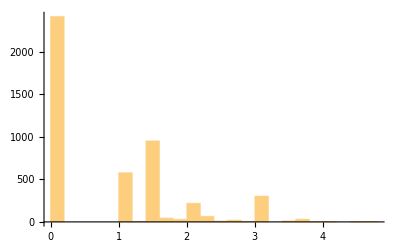

```mathematica
Histogram[Values[ruleDimensions]]
```

```mathematica
maxRule=Last[Keys[ruleDimensions]]
```

{{1,2},{3,2}}→{{1,2},{3,2},{4,2}}

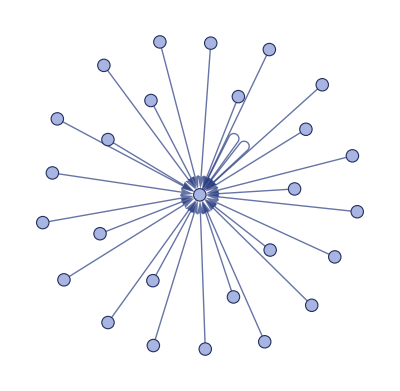

```mathematica
wm[maxRule, {{1,1},{1,1}}, 7, "FinalStatePlot"]
```

## Multiway graph of rule changes